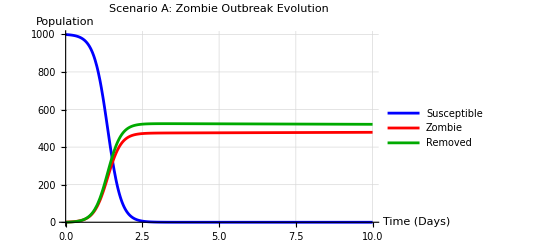

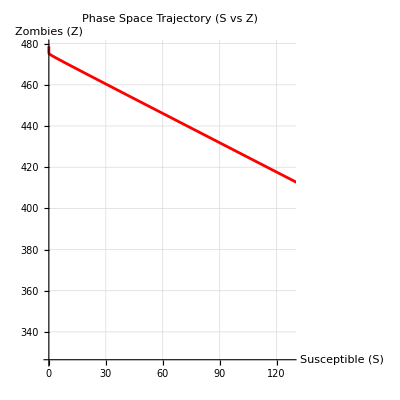

Symbolic Eigenvalues at DFE:

{0,1/2 (-1000 alpha+1000 beta-zeta-√(4000 beta zeta+(1000 alpha-1000 beta+zeta)^2)),1/2 (-1000 alpha+1000 beta-zeta+√(4000 beta zeta+(1000 alpha-1000 beta+zeta)^2))}

Numerical Eigenvalues for Scenario A:

{0,-0.00211059,4.50111}

RESULT: The DFE is UNSTABLE (Any zombie infection will spread).

```mathematica
(*PART 1:DEFINING THE SZR MODEL& BASIC SIMULATION*)(*Initialise the environment*)Clear["Global`*"]

(*1. Define the System of Differential Equations*)
(*s[t]:Susceptible,z[t]:Zombies,r[t]:Removed*)
equations={s'[t]==-beta*s[t]*z[t],z'[t]==beta*s[t]*z[t]-alpha*s[t]*z[t]+zeta*r[t],r'[t]==alpha*s[t]*z[t]-zeta*r[t],(*Initial Conditions*)s[0]==999,(*N-1*)z[0]==1,(*Patient Zero*)r[0]==0};

(*2. Define Parameters*)
(*beta:Transmission,alpha:Kill rate,zeta:Resurrection*)
paramsA={beta->0.0095,alpha->0.005,zeta->0.001};
tMax=10; (*Simulation duration in days*)

(*3. Solve Numerically using NDSolve*)
solA=NDSolve[equations/. paramsA,{s,z,r},{t,0,tMax}];

(*4. Plot Time Evolution*)
Plot[Evaluate[{s[t],z[t],r[t]}/. solA],{t,0,tMax},PlotStyle->{Blue,Red,Darker[Green]},PlotLegends->{"Susceptible","Zombie","Removed"},PlotLabel->"Scenario A: Zombie Outbreak Evolution",AxesLabel->{"Time (Days)","Population"},GridLines->Automatic]


(*PART 2:Phase space analyse*)

(*Visualizing the Trajectory of Humans vs Zombies*)
ParametricPlot[Evaluate[{s[t],z[t]}/. solA],{t,0,tMax},PlotStyle->{Red,Thickness[0.005]},AspectRatio->1,PlotLabel->"Phase Space Trajectory (S vs Z)",AxesLabel->{"Susceptible (S)","Zombies (Z)"},GridLines->Automatic,Epilog->{PointSize[Large],Green,Point[{999,1}],Red,Point[{0,1000}]}]



(*PART 3: Tunable combat Simulator*)

Manipulate[Module[{sol,Npop=1000},(*Dynamic Solution inside Manipulate*)sol=NDSolve[{S'[t]==-b*S[t]*Z[t],Z'[t]==b*S[t]*Z[t]-a*S[t]*Z[t]+zR*R[t],R'[t]==a*S[t]*Z[t]-zR*R[t],S[0]==Npop-1,Z[0]==1,R[0]==0},{S,Z,R},{t,0,time}];
(*Dynamic Plotting*)Column[{Plot[Evaluate[{S[t],Z[t],R[t]}/. sol],{t,0,time},PlotRange->{{0,time},{0,Npop}},PlotStyle->{Blue,Red,Darker[Green]},PlotLegends->{"Susceptible","Zombie","Removed"},ImageSize->400,AxesLabel->{"Time","Pop"}],(*Phase Space showing the "Doomsday" attractor*)ParametricPlot[Evaluate[{S[t],Z[t]}/. sol],{t,0,time},PlotRange->{{0,Npop},{0,Npop}},AspectRatio->1,AxesLabel->{"Susceptible","Zombies"},PlotStyle->Red,ImageSize->300,PlotLabel->"Phase Portrait"]}]],(*Controls/Sliders*){{b,0.0095,"Infection Rate (beta)"},0.001,0.05},{{a,0.005,"Kill Rate (alpha)"},0.000,0.05},{{zR,0.001,"Resurrection (zeta)"},0.000,0.1},{{time,15,"Simulation Days"},5,50}]



(*PART 4:STABILITY ANALYSIS (Jacobian& Eigenvalues)*)
(*Define the Symbolic Jacobian Matrix*)
(*J={{dS/dS,dS/dZ,dS/dR},...}*)
jacobianMatrix={{-beta*Z,-beta*S,0},{(beta-alpha)*Z,(beta-alpha)*S,zeta},{alpha*Z,alpha*S,-zeta}};

(*Define the Disease Free Equilibrium (DFE) point:S=N,Z=0,R=0*)
dfe={S->1000,Z->0,R->0};

(*Calculate Eigenvalues at DFE*)
eigenvalues=Eigenvalues[jacobianMatrix/. dfe];

Print["Symbolic Eigenvalues at DFE:"];
Print[eigenvalues];

(*Numerical check for Scenario A parameters*)
numEigenvalues=eigenvalues/. paramsA/. dfe;
Print["Numerical Eigenvalues for Scenario A:"];
Print[numEigenvalues];

(*Stability Logic Check*)
If[Max[Re[numEigenvalues]]>0,Print["RESULT: The DFE is UNSTABLE (Any zombie infection will spread)."],Print["RESULT: The DFE is STABLE (Infection dies out naturally)."]]
```